```mathematica
rInner=0.55;
rOuter=0.76;
```

```mathematica
OmegaSqNAdj[x_,y_]:=If[0.5<(x^2+y^2)^0.5<1,OmegaSqN[(x^2+y^2)^0.5,ArcCos[y/(x^2+y^2)^0.5]][[1]],0]
```

```mathematica
OmegaSq0SolAdj[x_,y_]=If[rInner<(x^2+y^2)^0.5<rOuter,OmegaSq0Sol[(x^2+y^2)^0.5],0];
OmegaSq2SolAdj[x_,y_]=If[rInner<(x^2+y^2)^0.5<rOuter,OmegaSq2Sol[(x^2+y^2)^0.5],0];

OmegaSqSolAdj[x_,y_]=If[rInner<(x^2+y^2)^0.5<rOuter,OmegaSq0SolAdj[x,y]+OmegaSq2SolAdj[x,y]*(y^2/(x^2+y^2)),OmegaSqNAdj[x,y]];
```

```mathematica
OmegaSq0FitAdj[x_,y_]=If[rInner<(x^2+y^2)^0.5<rOuter,OmegaSq0Fit[(x^2+y^2)^0.5],0];
OmegaSq2FitAdj[x_,y_]=If[rInner<(x^2+y^2)^0.5<rOuter,OmegaSq2Fit[(x^2+y^2)^0.5],0];

OmegaSqFitAdj[x_,y_]=If[rInner<(x^2+y^2)^0.5<rOuter,OmegaSq0FitAdj[x,y]+OmegaSq2FitAdj[x,y]*(y^2/(x^2+y^2)),OmegaSqNAdj[x,y]];
```

```mathematica
FreqNAdj[x_,y_]=OmegaSqNAdj[x,y]^0.5;
FreqSolAdj[x_,y_]=OmegaSqSolAdj[x,y]^0.5;
FreqFitAdj[x_,y_]=OmegaSqFitAdj[x,y]^0.5;
```

```mathematica
FittingCircumference=Graphics[Circle[{0,0},rOuter]];
FittingCircumference2=Graphics[Circle[{0,0},rOuter ]];
ConvectiveBorder=Graphics[{Thickness[0.01],Black,Opacity[0.6],Circle[{0,0},0.71]}];
ExternalBorder=Graphics[{Thick,Circle[{0,0},0.995]}];
ExternalBorder2=Graphics[{Thick,Circle[{0,0},0.995*rOuter]}];
ExternalBorder3=Graphics[{Thick,Circle[{0,0},0.995*rEnd]}];
InternalBorder0=Graphics[{Thick,Circle[{0,0},rInner]}];
InternalBorder=Graphics[{Thick,Circle[{0,0},rInner]}];
InternalBorder3=Graphics[{Thick,Circle[{0,0},rStart]}];
```

```mathematica
PTrue=ContourPlot[FreqNAdj[x,y],{x,0,1},{y,0,1},Contours->60, ColorFunction->"Rainbow",ContourStyle->Directive[White,Opacity[0.2]],RegionFunction->Function[{x,y,z},rInner<(x^2+y^2)^0.5<1],PlotLegends->Automatic];
PFit=ContourPlot[FreqFitAdj[x,y],{x,0,1},{y,0,1},Contours->60,ColorFunction->"Rainbow",ContourStyle->Directive[White,Opacity[0.2]],RegionFunction->Function[{x,y,z},rInner<(x^2+y^2)^0.5<1],PlotLegends->Automatic];
```

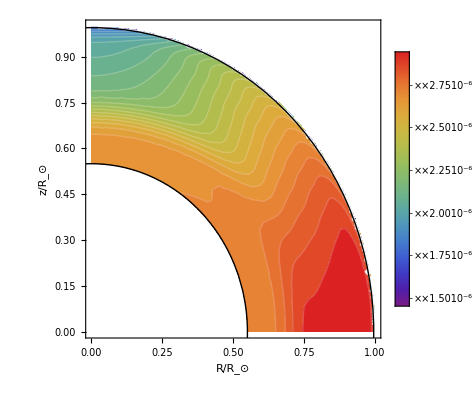

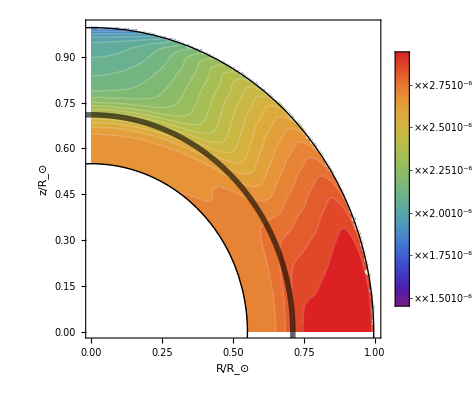

```mathematica
Show[PTrue,ExternalBorder,InternalBorder0,FrameLabel->{"R/R_⊙","z/R_⊙","GONG DATA"},BaseStyle->{FontWeight->"Bold",FontSize->14}]
Show[PTrue,ExternalBorder,InternalBorder0,ConvectiveBorder,FrameLabel->{"R/R_⊙","z/R_⊙","GONG DATA"},BaseStyle->{FontWeight->"Bold",FontSize->14}]
Show[PFit,FittingCircumference2,InternalBorder,ExternalBorder,FrameLabel->{"R/R_⊙","z/R_⊙","GONG DATA & FIT"},BaseStyle->{FontWeight->"Bold",FontSize->14}];
```

```mathematica
N[(2*Pi)/(2.4*10^-6)/86400]
```

30.3009

```mathematica
PTruePartial=ContourPlot[FreqNAdj[x,y],{x,0,rOuter},{y,0,rOuter},Contours->100, ColorFunction->"Rainbow",ContourStyle->Directive[White,Opacity[0.9]],RegionFunction->Function[{x,y,z},rInner<(x^2+y^2)^0.5<rOuter],PlotLegends->Automatic];
PFitPartial=ContourPlot[FreqFitAdj[x,y],{x,0,rOuter},{y,0,rOuter},Contours->100,ColorFunction->"Rainbow",ContourStyle->Directive[White,Opacity[0.9]],RegionFunction->Function[{x,y,z},rInner<(x^2+y^2)^0.5<rOuter],PlotLegends->Automatic];
```

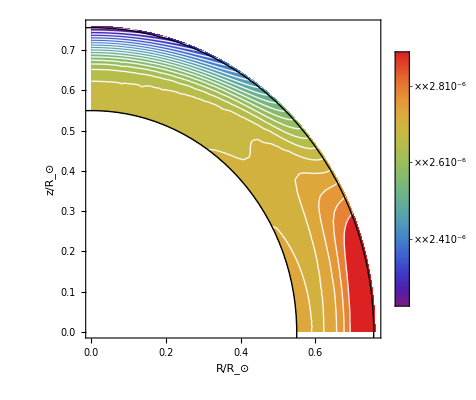

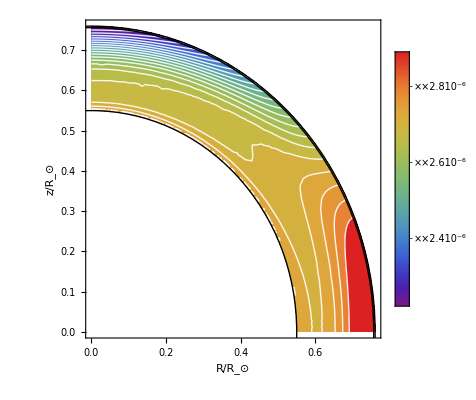

```mathematica
Show[PTruePartial,ExternalBorder2,InternalBorder0,FrameLabel->{"R/R_⊙","z/R_⊙","GONG DATA"},BaseStyle->{FontWeight->"Bold",FontSize->14}]
Show[PFitPartial,FittingCircumference2,InternalBorder,ExternalBorder2,FrameLabel->{"R/R_⊙","z/R_⊙","FIT"},BaseStyle->{FontWeight->"Bold",FontSize->14}]
```